0.0756879

11.4911

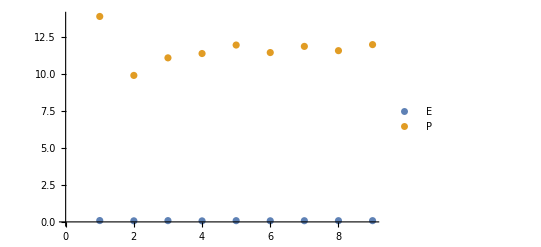

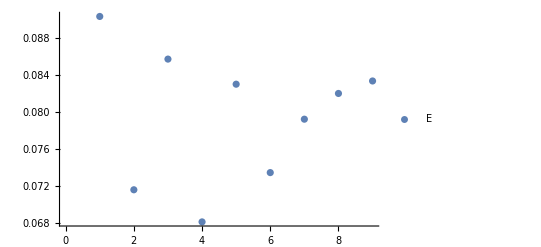

```mathematica
import=Import["Google Drive/jie_programs/QHlattice/auto","Table"];
n=Length[import];
autoE=Table[import[[i]][[4]],{i,n}]/n//Total
autoP=Table[import[[i]][[7]],{i,n}]/n//Total

import=Import["Google Drive/jie_programs/QHlattice/auto_jie","Table"];
n=Length[import];
step=Table[import[[i]][[1]],{i,n}];
autoE=Table[import[[i]][[2]],{i,n}];
autoP=Table[import[[i]][[3]],{i,n}];
dataE=Table[{step[[i]],autoE[[i]]},{i,n}];
dataP=Table[{step[[i]],autoP[[i]]},{i,n}];
ListPlot[{dataE, dataP}, PlotLegends->{"E","P"}]
ListPlot[dataE, PlotLegends->{"E"}]
```